### Minkowski sprinkling for n dimensions

#### Causal complete

```mathematica
CreateCSSeriesMinkowskiSeries[n_,d_]:=Module[{s,R,metric,pts,pairs,graphs},
metric=Flatten[{1,ConstantArray[-1,d-1]}];
s= IntegerPart[n^(1/d)];
R=Cuboid[ConstantArray[0,d],ConstantArray[s,d]];
pts=SortBy[RandomPoint[R,n],First];
pairs=Select[ Tuples[pts,{2}],#[[All,1]][[1]]<#[[All,1]][[2]]&];
graphs=Graph[Rule@@@pairs[[Flatten[Position[Total[(#[[2]]-#[[1]])^2.metric]&/@pairs,_?(#≥ 0&)]]]]];
graphs=Table[Subgraph[graphs,Subsets[Take[pts,i],{2}]],{i,1,Length[pts]}];
AdjacencyMatrix[#]&/@Select[graphs,EmptyGraphQ[#]==False&]];
```

#### Transitive reduced

```mathematica
CreateCSSeriesMinkowskiSeriesTransReduction[n_,d_]:=Module[{s,R,metric,pts,pairs,graphs},
metric=Flatten[{1,ConstantArray[-1,d-1]}];
s= IntegerPart[n^(1/d)];
R=Cuboid[ConstantArray[0,d],ConstantArray[s,d]];
pts=SortBy[RandomPoint[R,n],First];
pairs=Select[ Tuples[pts,{2}],#[[All,1]][[1]]<#[[All,1]][[2]]&];
graphs=Graph[Rule@@@pairs[[Flatten[Position[Total[(#[[2]]-#[[1]])^2.metric]&/@pairs,_?(#≥ 0&)]]]]];
graphs=Table[Subgraph[graphs,Subsets[Take[pts,i],{2}]],{i,1,Length[pts]}];
AdjacencyMatrix[TransitiveReductionGraph[#]]&/@Select[graphs,EmptyGraphQ[#]==False&]];
```

```mathematica
CreateCSSeriesMinkowskiV4Series[10,2]
```

{SparseArray[<1>, {3, 3}],SparseArray[<1>, {4, 4}],SparseArray[<2>, {5, 5}],SparseArray[<5>, {6, 6}],SparseArray[<10>, {7, 7}],SparseArray[<13>, {8, 8}],SparseArray[<17>, {9, 9}],SparseArray[<23>, {10, 10}]}

```mathematica
CreateCSSeriesMinkowskiV4SeriesTransReduction[10,4]
```

{SparseArray[<1>, {3, 3}],SparseArray[<1>, {3, 3}],SparseArray[<2>, {4, 4}],SparseArray[<2>, {4, 4}]}

### Casual set interval (causal diamond)

```mathematica
CreateMinkowskiInterval[n_,d_,pts_]:=Module[{s,R,metric,pairs,start,source,sink,ptsfut,ptspast,ptsall,graphs},
metric=Flatten[{1,ConstantArray[-1,d-1]}];
start=RandomInteger[Length[pts]];
source=pts[[start]];
sink=pts[[RandomInteger[{start,Length[pts]}]]];
ptsfut=Select[pts,#[[1]]>source[[1]]&&#[[1]]<sink[[1]]&];
pairs=Select[ Table[{source,i},{i,ptsfut}],#[[All,1]][[1]]<#[[All,1]][[2]]&];
pairs=pairs[[Flatten[Position[Total[(#[[2]]-#[[1]])^2.metric]&/@pairs,_?(#≥ 0&)]]]];
ptsfut=Union[Flatten[pairs,1]];
ptspast=Select[pts,#[[1]]<sink[[1]]&&#[[1]]>source[[1]]&];
pairs=Select[ Table[{i,sink},{i,ptspast}],#[[All,1]][[1]]<#[[All,1]][[2]]&];
pairs=pairs[[Flatten[Position[Total[(#[[2]]-#[[1]])^2.metric]&/@pairs,_?(#≥ 0&)]]]];
ptspast=Union[Flatten[pairs,1]];
ptsall=Union[Intersection[ptspast,ptsfut],{source},{sink}];
pairs=Select[ Tuples[ptsall,{2}],#[[All,1]][[1]]<#[[All,1]][[2]]&];
graphs=Graph[Rule@@@pairs[[Flatten[Position[Total[(#[[2]]-#[[1]])^2.metric]&/@pairs,_?(#≥ 0&)]]]]]
]
```

```mathematica
CreateMinkowskiIntervals[n_,d_,iter_]:=Module[{pts},
pts=CreateMinkowskiCS[n,d];
pts=SortBy[pts,First];
Select[Table[CreateMinkowskiInterval[n,d,pts],{i,iter}],!EmptyGraphQ[#]&]
]
```

```mathematica
CreateMinkowskiCS[n_,d_]:=Module[{s,R,t,r,limits,pts,pairs,graphs,metric,reg,omegalist,freg,preg,Region},
metric=Flatten[{1,ConstantArray[-1,d-1]}];
s= IntegerPart[n^(1/d)];
R=Cuboid[ConstantArray[0,d],ConstantArray[s,d]];
pts=RandomPoint[R,n]
]
```

### Estimate ordering fraction of causal intervals

```mathematica
orderingfract[d_]:=Gamma[d+1]Gamma[d/2]/(4 Gamma[3d/2])
```

#### 2 D

```mathematica
2 orderingfract[2]
```

1/2

```mathematica
glist=CreateMinkowskiIntervals[1000,2,1000];
```

Set::setraw: Cannot assign to raw object {{0.112677,26.447},{0.151375,11.1845},{0.152223,20.9455},{0.261603,3.03385},{0.276878,11.0044},«41»,{1.49458,24.956},{1.5415,5.26054},{1.5436,19.0936},{1.69863,9.70892},«950»}.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
data={#[[1]],#[[2]]/Binomial[#[[1]],2]}&/@Select[{VertexCount[#],EdgeCount[#]}&/@glist,#[[2]]>0&];
```

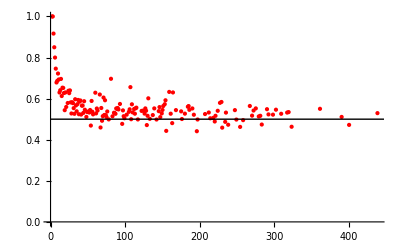

```mathematica
Show[ListPlot[Table[{i,Mean[Union[Select[data,#[[1]]==i&]][[All,2]]]},{i,Union[#[[1]]&/@data]}],PlotRange->{0,1},PlotStyle->{PointSize[Large],Red}],Graphics[{Thick,Line[{{0,0.5},{1000,0.5}}]}]]
```

```mathematica
glist=Select[Table[CreateMinkowskiInterval[5000,3],{i,2000}],!EmptyGraphQ[#]&];
```

```mathematica
data={#[[1]],#[[2]]/Binomial[#[[1]],2]}&/@Select[{VertexCount[#],EdgeCount[#]}&/@glist,#[[2]]>0&];
```

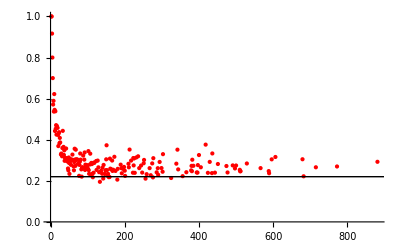

```mathematica
Show[ListPlot[Table[{i,Mean[Union[Select[data,#[[1]]==i&]][[All,2]]]},{i,Union[#[[1]]&/@data]}],PlotRange->{0,1},PlotStyle->{PointSize[Large],Red}],Graphics[{Thick,Line[{{0,0.22},{1000,0.22}}]}]]
```

```mathematica
glist=Select[Table[CreateMinkowskiInterval[5000,4],{i,2000}],!EmptyGraphQ[#]&];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
data={#[[1]],#[[2]]/Binomial[#[[1]],2]}&/@Select[{VertexCount[#],EdgeCount[#]}&/@glist,#[[2]]>0&];
```

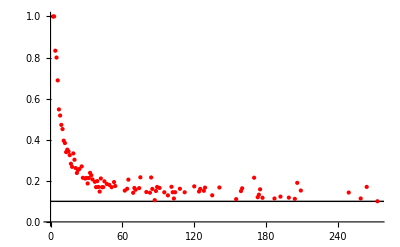

```mathematica
Show[ListPlot[Table[{i,Mean[Union[Select[data,#[[1]]==i&]][[All,2]]]},{i,Union[#[[1]]&/@data]}],PlotRange->{0,1},PlotStyle->{PointSize[Large],Red}],Graphics[{Thick,Line[{{0,0.1},{1000,0.1}}]}]]
```